```mathematica
$Path=Join [$Path,{NotebookDirectory[]}];
Get["MathSVM`"]
Needs["PlotLegends`"]//Quiet;
(*{fTr,yTr,fTe,yTe}=loadData ["banana.mat"];*)
```

SVM Package Loaded

# A hands-on introduction to Support Vector Machines

Feb 3, 2014

Marco Fornoni

### Abstract

Nowadays computers can be trained to perform a variety of tasks, traditionally associated with intelligence. Recognizing people, classifying webpages, recognizing human speech, performing online trading, are just a few examples of tasks that can be performed by machines. 
Behind this very diverse set of abilities there is a branch of computer science and artificial intelligence, called machine learning, which deals with the problem of constructing and studying systems able to learn from data. In a supervised machine learning setting, problems are directly specified by sets of input data, with associated desired outputs. The goal of a learning machine is then to learn a mathematical model able to reproduce the desired output on the training data, while preserving generalization abilities on unseen data. This approach results to be very useful when the functional dependency of the output w.r.t. the input is not known, or is too complex to be modeled exactly.

One of the most successful machine learning tools that is widely used to solve classification and regression problems is called Support Vector Machine (SVM) [1].  The key assumption of this model is that training and testing samples are generated i.i.d. according to an unknown but fixed distribution. Given a set of i.i.d.  training instances {(x_1,y_1),(x_2,y_2)_(,…,)(x_n,y_n)}, where x_i∈X⊂ℝ^d is an input and y_i∈ℝ is the desired output, a SVM predicts using a real valued function f_(w,b)X⊂ℝ^d→ℝ, parametrized by a vector w ϵ ℝ^d and a scalar b∈ℝ (bias). This prediction function f_(w,b) is chosen to maximize a quantity called margin and it is linear. Kernel methods can be used to extend SVM to the non-linear setting, without modifing the analysis and implementation of the method.

The goal of this notebook is to present the very basic theory of linear classifiers, max-margin classifiers and Support Vector Machines and to explore the use of Mathematica to solve the optimization problems that arise. Following the presentation in [1], this notebook explicitly derives, implements and compare several classifiers, demonstrating them on synthetic 2D-data generated by the user, with visualizations involving direct hyper-parameters manipulations. It can thus be considered a hands-on introduction to the topic.

## Section. Introduction

As computers are applied to address increasingly complicated problems, situations arise in which there is no known method to build a model able to produce a desired output, from a given set of inputs.
Consider the task of recognizing hand written digits. The goal is to estimate a function that will take numerical representation (e.g. a raster image) of an hand-written digit and that will output the identity of the digit in the image: 0, . . . , 9. At first glance, one would think that a possible way to address such problems could be to hard-code some rules to perform the recognition. Unfortunately, this approach would demand huge human efforts to analyze a representative dataset of digits and to find stable patterns that could be used for the recognition task. Moreover, due to the large variability in the hand writings, it may produce poor results when applied to digits produced by writers that were not considered during the rule making process. Finally, the skills acquired while addressing the digit recognition problem would not be transfered to other unrelated problems like, for example, automatically recognizing spoken words.
A more modern approach to tackle such problems is to use machine learning to design general pattern recognition algorithms and to study their generalization properties. These tools could then be applied to any pattern recognition problem (such as the above mentioned digit recognition and speach recognition problems), with a comparably very limited human effort.
Pattern recognition algorithms make use of a set of training examples of the form (x_i,y_i), where x_i∈ X⊂ ℝ^d is a numerical representation of an input instance and y_i∈ Y is an associated desired output. 
Suppose that the training examples are drawn from a given distribution ⅅ on X×Y. The goal of a pattern recognition algorithm is to automatically learn a function f_v:X→Y (where v is a parameter, or a set of parameters to be estimated) able to produce the desired output y_i on each training example x_i and to perform well on other (unseen) example drawn from the same distribution ⅅ.

One of the most powerful and widely used tools to solve pattern recognition tasks is the Support Vector Machine (SVM) [1]. Over the last 15 years, this class of algorithms have become the de facto standard in several fields. In this notebook we will present the basic theory of SVMs and present some simple implementations using Mathematica.
An outline of the notebook is as follows. In Section Section we introduce the basics concepts of linear classifiers. Section Section presents the theory of max-margin classifiers and the resulting algorithms and implementations. In Section Section we introduce Support Vector Machines, the related optimization tools and several implementations. Section Section finally discusses the usage of kernel methods to turn the SVM classifiers into non-linear ones, without any modification to the learning algorithms and the analysis. We conclude in Section Section , pointing out some possible extensions of this work.

## Section. Linear Classifiers

Suppose we are given a set of n training examples S≡{(x_i,y_i), i=1,…,n} drawn from a given distribution ⅅ on X×Y, where:

x_i∈X⊂ ℝ^d,y_i∈ Y;

X is called the input space;

Y is called the outcome (or decision) space.

In binary classification problems (problems with two classes), the decision space is defined asY≡{-1,1} and a linear classifier can be defined in the following way:

(ŷ)_i(w,b)=sign(f_(w,b)(x_i)),

where (ŷ)_i is the predicted label for a given sample x_i, using parametes  (w,b)ϵ ℝ^d×ℝ, while f_(w, b):X→ℝ is a parametric linear function, defined as

f_(w,b)(x)=w·x +b.

We refer to f_(w,b) as to the scoring function of the linear classifier, as it provides a classification score for each sample. For brevity, we also sometimes refer to f_(w,b) as to the classifier.
The geometry of this simple classifier can be understood by looking at the 2D visualization in the following figure. The points whose vector projection on w is grater than -b will be positively classified, while the others will be negatively classified. The equation w·x+b=0 thus defines a (hyper) plane separating the positively classified points from the negative ones.

-Graphics-"Geometry of a linear classifier."

Let Χ(r) be the indicator function of the predicate r and let h be a the scoring function of a linear classifier. A natural measure for the performance of a binary classifier is given by the 0/1 istantaneous error, which for a sample x_i can be written as

e(h,i)=Χ(y_i h(x_i)<0).

As it can be seen, if the sign of y_i and h(x_i) disagree, the prediction will be counted as erroneous and we will have e(h,i)=1. In the other case, if the sign of y_i and h(x_i) agree, the prediction will be considered correct and we will have e(h,i)=0.

Using the error function e(h,i), we can now define the risk functional err_ⅅ(h) of a classifier h over a distribution ⅅ as

err_ⅅ(h)=ⅅ{(x_i,y_i):e(h,i)==1},

which is the expected error rate of the classifier over the set of samples generated according to ⅅ. This quantity represents the true risk that a sample (x_i,y_i) generated according to ⅅ is missclassified by the classifier.
The so called “generalization ability” of a classifier can then be defined as its ability to have a low true risk on err_ⅅ(h), and thus have a low expected error on samples which were possibly not considered when constructing h (unseen samples).

Since the distribution ⅅ is often unknown, this quantity is not directly measurable. Moreover, the error function used by this functional is non-smooth, its gradient is zero and it is thus not very tractable, as can be seen in the following figure.

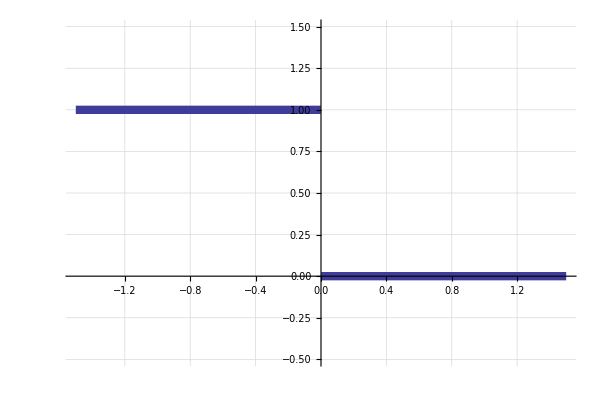
-Graphics-Error function e, as a function of: y_i h(x_i)

```mathematica
Labeled[Plot[err[x],{x,-1.5,1.5},PlotRange->{Full,{-.5,1.5}},AspectRatio->Automatic,Background->White,PlotStyle->{Thickness[.01]}],"Error function e, as a function of: y_i h(x_i)"]
```

## Section. Maximal-margin classifiers

### Margin-based Generalization Bounds

In the previous section we have introduced linear classifiers, the 0/1 error function e(h,i) and the risk functional err_ⅅ(h). Starting from these definitions, a more optimization-friendly performance measure can be obtained by using the definition of functional margin γ_i, of a classifier h over a sample (x_i,y_i):

γ_i=y_i h(x_i).

Note that whenever γ_i>0, we have e(h,i)=0 and the sample i is correcty classified, while if γ_i<0, we have e(h,i)=1 and the sample is missclassified. 
We can than define the minimal functional margin of a classifier using a scoring function h on a training set S, as

m_S(h)=min_((x_i,y_i)∈S) γ_i

Using this quantity we can now state without proving the following result from the Generalization Theory of max-margin classifiers [1].

Theorem 1. Let ℋ be the set of linear scoring functions having a unit weight vector w, on an input space X. For any probabilty distribution on X×{-1,1}, with support on a ball of radius R around the origin, with probability 1-δ over n random samples S, the error of any classifier using a scoring function h∈ℋ with a minimal margin m_S(h) ≥ γ is bounded by

err_ⅅ(h)≤ϵ=2/n((64 R^2)/γ^2 log ℯnγ/(4R)log (128 R^2)/γ^2+log 4/δ),

where γ∈ℝ^+and provided that n>2/ϵ and (64 R^2)/(^(γ^2))<n.
This bound tells us that the generalization ability of a linear classifier trained on a set S composed of n random samples drawn from 𝒟, is directly related to the minimum margin acheived by the classifier on the training set S. We also note that the generalization does not depend on the dimensionality of the input space X.
In other words, this theorem tells us that whenever w is normalized to one, a classifier with a large minimal functional margin γ will also have a low true risk on 𝒟 and thus perform well also on unseen samples drawn from 𝒟.

### Maximal margin classifier: hard margin

Recall that the functional margin on a sample was defined as γ_(i=)y_i h(x_i). For a linear classifiers this definition specializes to γ_i=y_i(w·x_i+b). This quantity obviously depends on the norm of w, as it is affected by any rescaling of w. In order to remove this dependency, instead of forcing w to be normalized to 1 (as in Theorem 1), we consider the geometric margin, which is the Euclidean distance of the point to the hyper-plane given by w·x+b=0 .
For any correctly classified sample (x_i,y_i), the geometric margin can be computed as

1/(‖w‖)y_i(w·x_i+b)=1/(‖w‖)|w·x_i+b|,

where y_i has the role of inverting the sign of the projection, in case the sample was negative. As we can see, this is basically a rescaled version of the functional margin defined above, making it independent from the norm of w.
The minimal geometric margin over a set of examples S can then be defined as

g_S(f_(w,b))=min_((x_i,y_i)∈S) 1/(‖w‖)y_i(w·x_i+b).

Using this definition and following the intuition provided by Theorem 1 (that we should select a classifier with a large minimal margin) we could thus define the following max-margin objective function, maximizing the generalization ability of the classifier

max_(w,b) 1/(‖w‖)min_((x_i,y_i)∈S) y_i(w·x_i+b),

for any linearly separable problem S (a problem for which there exist a linear scoring function f_(w,b) such that m_S(f_(w,b))>0).
This is a non-linear non-convex objective function, which is very is difficult to optimize. A way to ease the optimization could be to impose (‖w‖)^2=1 (as also suggested also by Theorem 1), however this would result in a problem with quadratic constraints (Second Order Cone Programming), which is still not immediate to solve.
Alternatively, since we are considering a linearly separable dataset S, instead of normalizing w by imposing (‖w‖)^2=1, we could equivalently rescale it until m_S(f_(w,b))=1, resulting in the following optimization problem

max_(w,b) 1/(‖w‖)
s.t. min_((x_i,y_i)∈S) y_i(w·x_i+b)=1.

By noting that the maximization of 1/(‖w‖) can be equivalently replaced by a minimization of (‖w‖)^2 and that the constraint min_((x_i,y_i)∈S) y_i(w·x_i+b)=1 can be replaced by y_i(w·x_i+b)≥1,∀(x_(i,)y_i)∈S, we obtain the final objective function of the maximal margin classifier

min_(w,b) w·w
s.t. 1-y_i(w·x_i+b)≤0,   ∀(x_(i,)y_i)∈S.

The classifier obtained by solving problem (DisplayFormulaNumbered) is also called hard-margin classifier, as it requires linear separability of the data, imposing a functional margin of 1, for all the training points. Indeed, with this approach any feasible solution (w,b) will correctly classify all the training points with a functional margin of at least one. The minimal geometric margin of the optimal classifier can thus be computed as g_S(f_(w,b))=min_((x_i,y_i)∈S) 1/(‖w‖)y_i(w·x_i+b)=1/(‖w‖)min_((x_i,y_i)∈S) y_i(w·x_i+b) =1/(‖w‖) .

#### Implementation in Mathematica

It can also be noticed that (DisplayFormulaNumbered) has the form of a standard Quadratic Programming (QP) problem (a quadratic objective function, with linear constraints). It can thus be solved using the Mathematica QP solver, as showcased by the following code snippet:

```mathematica
trainMaxMargin[fTr_,yTr_]:=Module[
{results,model,margin,nTr,fTr2,d,w,v,b,i,sol,cnstr},
{nTr,d}=Dimensions[fTr];
w=Table[Subscript[v, i],{i,d}];
cnstr=And@@(#<=0&/@Flatten@(1-(fTr.w+b)yTr));
sol=FindMinimum[{w.w,cnstr},Join[w,{b}], Compiled->True, 
Method -> "QuadraticProgramming"];
model=({w,b}/.sol[[2]]);
margin=1/Sqrt[sol[[1]]];
results={model,margin}
];
```

As it can be seen, the basic max-margin classifier can be implemented in Mathematica using just a few lines of code. 
Here is an example, using the SVM package imported in the initialization cell of the notebook. First we make use of the function createData in order to draw an arbitrary training set. After calling this function, it is possible to draw samples in the plot by clicking and dragging. A single click in any point of the plot will change the color/label of the samples that are going to be drawn subsequently.

```mathematica
createData[]
```

-Graphics-

The 2D coordinates and associated lables of the drawn points are then obtained by calling the function {fTr,yTr,fTe,yTe}=getTrTeData[trPerc], which also randomly split the data into a training and a testing set, with a specific percentage used for training.
In the following we will use a 30/70% training/testing split.
Finally, the classification algorithm can be run on the selected dataset by using the command runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainMaxMargin] . This command will produce a plot reporting, in the title, the training error, the testing error and the achieved minimal geometric margin g_s(h) (the Euclidean distance of the closest point to the separation surface). The training points are represented with a large marker, while the testing points are represented by a small marker.

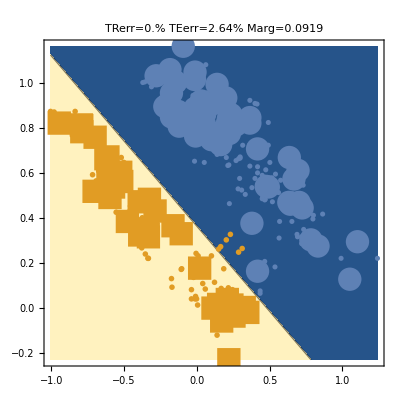

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
results=runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainMaxMargin]
```

As it can be seen, if the training data is linearly separable (if there exists an hyperplane separating the two classes), the max-margin classifier will always return the hyperplane maximizing the minimal geometric margin g_s(h) between the two classes.
Unfortunately, if the training data is not linearly separable this learning algorithm will fail to find a feasible solution (try drawing a non-linearly separable dataset for a direct proof). Moreover, while margin-maximization is a desirable property for generalization, when the training and the testing datasets do not exactly follow the same distribution (which is often the case due to noise, or too small training sets), exact margin maximization can result in poor testing performances. A way to address these problems is represented by the so-called “soft-margin” classifiers, introduced in the following Subsection.

### Maximal margin classifier: soft margin

The formulation introduced above is designed for linearly separable problems. However, it often happens that a dataset does not satisfy this condition, or it is difficult to know in advance whether it holds or not. In case the problem does not turn out to be linearly separable, the max-margin learning algorithm will fail to find a solution satisfying the constraints, leaving us without a solution.
In order to addess this problem, soft-margin classifiers have been designed [1] to allow the algorithm to violate the constraints y_i(w·x_i+b)≥1-ξ_i, by an amount ξ_i (called slack variable) as little as possible.
In this case, the optimization problem can be written as:

min_(w,b,ξ) w·w +C ∑_(i=1)^n ξ_i
s.t. 1-ξ_i-y_i(w·x_i+b)≤0,   i=1,…,n,
          ξ_i≥0,                                      i=1,…,n

where C tunes the importance of the slack variable minimization, w.r.t. the margin maximization. A big value of C will push the optimization algorithm to find a hyperplane on which all the points are correctly classified with margin 1, while lower value of C will allow the learning algorithm to commit margin - or decision - mistakes on some samples, without heavily affecting the decision boundary.

In this case the minimal geometric margin g_S(f_(w,b)) of the optimal classifier cannot be computed simply as 1/(‖w‖), since there is no guarantee anymore that y_i(w·x_i+b)≥ 1. Nonetheless for all the points for which y_i(w·x_i+b)<1 we will have y_i(w·x_i+b)=1-ξ_i, while for the others we will have ξ_i=0. Therefore, the minimal geometric margin can be computed exactly using g_S(f_(w,b))=1/(‖w‖)(1-max_i ξ_i). For linearly separable datasets and with C→∞, we will have max_i ξ_i=0 and the margin obtained with this approach will correspond to the one obtained by the max-margin classifier. On the other hand, on non linearly separable datasets, we might have ξ_i>1, resulting in negative geometric margins. In this case the geometric margin behaves as a signed Euclidean distance, with a negative sign meaning that the problem is not separable.

#### Implementation in Mathematica

Even if at a first glance the optimization problem (DisplayFormulaNumbered) does not look very friendly, it can be shown to still be a QP program. It can thus be again directly solved using the Mathematica QP solver, as shown by the following code snippet:

```mathematica
trainSoftMargin[fTr_List,yTr_List,regC_]:=Module[
{results,model,margin,nTr,fTr2,d,w,v,b,xi,x,i,sol,obj,cnstr},
{nTr,d}=Dimensions[fTr];
w=Table[Subscript[v, i],{i,d}];
xi=Table[Subscript[x, i],{i,nTr}];
cnstr=And@@(#<=0&/@Flatten@(1-xi-(fTr.w+b)yTr)) &&
And@@(#>=0&/@Flatten@xi);
obj=w.w+regC Total[xi];
sol=FindMinimum[{obj,cnstr},Join[w,{b},xi], Compiled->True, 
Method -> "QuadraticProgramming"];
model=({w,b,xi}/.sol[[2]]);
sol[[1]];
margin=(1-Max[model[[3]]])/Norm[model[[1]]];
results={model,margin}
];
```

As before, we report here an example of usage, where createData[] is called in order to draw a dataset and  {fTr,yTr,fTe,yTe}=getTrTeData[trPerc] is used to obtain the coordinates of the training and the testing points, using a 30%/70% training/testing split.

```mathematica
createData[]
```

-Graphics-

This time, in order to use the soft-margin classifier with a regularization parameter C, we will use the command  runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainSoftMargin[#1, #2, C]&]. In this case the classifier funtion is created as an anonymous function with two parameters (corresponding to fTr and yTr - see the documentation -) while the third parameter, the regularization coefficientC is fixed. Finally, in order to show the behavoir of the algorithm when varying the regularization parameter, we will also make use of the Mathematica function Manipulate to dynamically adjust the plot while varying the parameter C.

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainSoftMargin[#1,#2,10^c]&],{c,0,5,.2}]
```

As it is possible to see, in agreement with the theory when C→∞, the solution returned by soft-margin classifier reduces to the one of the max-margin classifier. On the other hand, reducing C might results in the max-margin principle being violated, resulting in a different separation hyperplane. When the noise in the data is high, this might result in better performance on unseen samples.

### Maximal margin classifier: hinge-loss

An interesting property of the formulation introduced in the previous sub-section is that, by using the fact that the objective function is minimizing w.r.t. ξ and performing a simple case analysis, it is possible to see that for any (w,b):

whenever 1-y_i(w·x_i+b)≤0, then ξ_i=0 (no additional slack is necessary to satisfy the constraints);

whenever 1-y_i(w·x_i+b)>0, then ξ_i=1-y_i(w·x_i+b) (the minimal ξ_i satisfying the constraints).

We can thus write a closed form solution for ξ_i as a function of (w,b)

ξ_i=(|1-y_i(w·x_i+b)|)_+,

where |x|_+=max(x,0).  By construction, for any given (w,b) this choice of ξ_i ensures that all the constraints are satisfied. We can thus subsitute for ξ_i in the objective function and remove the constraints, obtaining the following optimization problem:

min_(w,b) w·w +C ∑_(i=1)^n (|1-y_i(w·x_i+b)|)_+

This is a non-smooth unconstrained convex optimization problem, which can be solved by using simple sub-gradient descent procedures.  As before, the minimal geometric margin can be computed exactly using g_S(f_(w,b))=1/(‖w‖)(1-max_i ξ_i), where in this case ξ_i=(|1-y_i(w·x_i+b)|)_+. We can also equivalently compute it using its definition, whichever is faster in the implementation.

Recalling that the functional margin was defined as γ_i=y_i f_(w,b)(x_i) and the 0/1 error function was defined as Χ(y_i f_(w,b)(x_i)<0), we can see that both the 0/1 error and the constraints violation ξ_i=(|1-y_i f_(w,b)(x_i)|)_+ (often refered to as hinge-loss) can be expressed as a function of γ_i. Moreover we have

Χ(γ_i<0)≤(|1-γ_i|)_+,

as it can also be seen in the following figure.

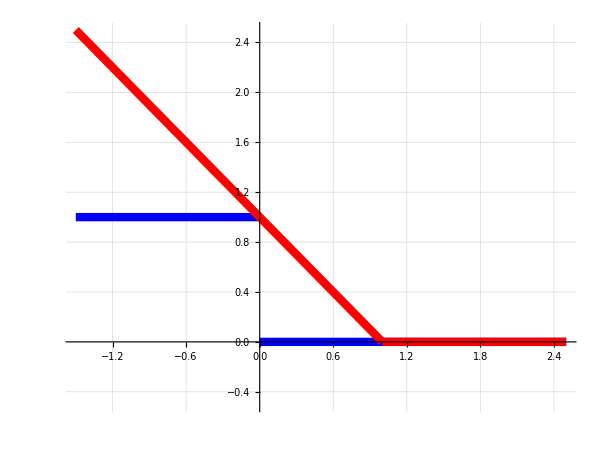
-Graphics-Hinge Loss and istantaneous error, as a function of the margin.

```mathematica
Labeled[Plot[{err[x],hinge[x]},{x,-1.5,2.5},PlotLegend->{"0/1 Error","Hinge Loss"},LegendPosition->{.5,.2},LegendShadow->{.02,-.02},LegendSize->{0.4,0.2},PlotRange->{Full,{-.5,2.5}},AspectRatio->Automatic,Background->White,PlotStyle->{{Thickness[.01],Blue},{Thickness[.01],Red}}],
"Hinge Loss and istantaneous error, as a function of the margin."]
```

The hinge loss is thus clearly a convex piecewise-linear upperbound of the 0/1 error function. Using this intuition, the hinge-loss classifier objective function can be virtually decomposed in two parts:

a “regularizer” w·w, named in this way because of its role in favoring general solutions

a weighted loss function C ∑_(i=1)^n (|1-y_i(w·x_i+b)|)_+, measuring the hinge-loss on every sample

#### Implementation in Mathematica

As before, we report here the code snippet of this implementation

```mathematica
hinge[x_]:=Piecewise[{{1-x,1-x>0}},0];

trainSoftMarginHinge[feats_List,labels_List,regC_]:=Module[
{results,model,margin,b,d,nTr,v,w,regularizer,loss,obj,sol},
{nTr,d}=Dimensions[feats];
w=Table[Subscript[v, i],{i,1,d}];
regularizer=w.w;
loss=Total[hinge@@@(labels (feats.w+b))];
obj=regularizer + regC loss;
sol=FindMinimum[obj, Join[w,{b}]]//Quiet;
model=({w,b}/.sol[[2]]);
margin=(Min[(labels (feats.model[[1]]+model[[2]]))])/Norm[model[[1]]];
results={model,margin}
];
```

An example of usage is as follow

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainSoftMarginHinge[#1,#2,10^c]&],{c,0,5,.2}]
```

As it is possible to see, the behavior of this classifier is very similar to the one of the original soft-margin algorithm (though the solution might slightly differ, for numerical reasons).

### Minimizing the 0/1 error

For what we said above, soft-margin maximization - and thus good generalization abilities - can be acheived through the minimization of the regularized hinge loss function: w·w +C ∑_(i=1)^n (|1-y_i(w·x_i+b)|)_+.  On the other hand, we have also seen that the hinge-loss is a convex piecewise-linear upper-bound to the 0/1 error, which ultimately is the quantity that we care about. What would happen if we replace  the hinge-loss in this regularized objective function, with a 0/1 error function?

#### Implementation in Mathematica

We can verify this by using the numerical optimization abilities of Mathematica (NMinimize) to solve

min_(w,b) w·w +C ∑_(i=1)^n Χ(y_i(w·x_i+b)<0),

Note that, although the objective function still includes a regularizer, the indicator function Χ does not measure the margin obtained by w, but only the 0/1 error. In Mathematica we can minimize this function for example, by asking NMinimize to perform a random search, as shown in the following code snippet

```mathematica
trainZeroOneError[c_,feats_,labels_]:=Module[
{results,model,margin,b,d,nTr,v,w,regularizer,loss,obj,sol},
{nTr,d}=Dimensions[feats];
w=Table[Subscript[v, i],{i,1,d}];
regularizer=w.w;
loss=Total[err@@@(labels (feats.w+b))];
obj=regularizer + c loss;
sol=NMinimize[obj, Join[w,{b}], Method->"RandomSearch"];
model=({w,b}/.sol[[2]]);
margin=1/Norm[model[[1]]](Min[(labels (feats.model[[1]]+model[[2]]))]);
results={model,margin}
];
```

Following is an example of usage of this code

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainZeroOneError[#1,#2,10^c]&],{c,0,10,.2}]
```

As it is possible to see Mathematica may be able to find an hyperplane minimizing the training 0/1 error. However, not only the optimization is much harder (as the objective function has always sub-gradient 0) but, more importantly, without promoting any margin maximization the generalization abilities of the classifier are clearly negatively affected. This in turn results in a high testing error rate.

## Section. Support Vector Machines

In the previous Section we introduced the basic theory of max-margin classifiers. A Support Vector Machine is basically a max-margin classifier (hard or soft-margin) trained in a different way. In this section we will first briefly introduce the convex optimization theory [1] necessary to derive the SVM algorithm, and then perform the derivations necessary to obtain SVMs and finally present the resulting implementations.

### Convex Optimization Theory

Suppose we are given an optimization problem of the form

min_w f(w),         w∈Ω⊂ℝ^d
s.t. g_i(w)≤0, i=1,…,n
	 h_i(w)=0, i=1,…,m

where f, g_i,i=1,…,n and h_i, i=1,…,m,  are a set of real functions defined on a domain Ω⊂ℝ^d . This problem is refered to as the primal problem.

The generalized Lagrangian of the minimization problem (DisplayFormulaNumbered) is defined as

L(w,α,β)=f(w)+ ∑_(i=1)^n α_i g_i(w)+∑_(i=1)^m β_i h_i(w)= f(w)+αᵀg(w)+βᵀh(w),

and the Lagrangian dual problem is defined as

max_(α,β)  θ(α,β)
s.t. α≥0,

where θ(α,β)= inf_(w∈Ω) L(w,α,β).
We will now cite the following important results from optimization theory.

Theorem 2 (Strong duality theorem). Let w^* be the solution of the of the primal optimization problem (DisplayFormulaNumbered) and let (α^*,β^*) be the solution of the Lagrangian dual problem (DisplayFormulaNumbered).
If Ω is convex and g_i,h_i are affine functions (i.e. g_i(w)=aᵀw-d), then f(w^*)=θ(α^*,β^*).

Theorem 3 (Karush–Kuhn–Tucker - KKT - optimality conditions). Given a primal optimization problem (DisplayFormulaNumbered), where Ω is convex, g_i,h_i are affine functions and f∈𝒞^1. Necessary and sufficient conditions for a point w^* to be an optimum are  the existence of α^*,β^* such that

(∂L(w,α^*,β^*))/(∂w)=0
(∂L(w^*,α^*,β))/(∂β)=0
α_i^*g_i(w^*)=0,i=1,…,n                (KKT complementarity condition)
g_i(w^*)≤0,i=1,…,n
α_i^*≥0,i=1,…,n

Theorem 2 tells us that if Ω is convex and g_i,h_i are affine functions, the optimal value of the primal problem can be obtained by solving the Lagrangian dual problem. Moreover, if f∈𝒞^1 Theorem 3 gives us the conditions characterizing the solution of both the primal and the dual problems. For example, the first condition in (DisplayFormulaNumbered) provides a way to compute θ(α^*,β^*), as it is showcased below for the SVM optimization problem.

### Support Vector Machines

Support Vector Machines arise when applying the convex optimization theory outlined above, to the max-margin classifiers introduced in Section Section.

#### Hard-margin SVM

The generalized Lagrangian of the optimization problem for the max-margin classifier (in eq. (DisplayFormulaNumbered)) is given by

L(w,b,α)=1/2(‖w‖)^2 + ∑_(i=1)^n α_i(1-y_i(w·x_i+b)),

where, for simplicty we have divided the squared norm of w by 1/2. The objective function in eq. (DisplayFormulaNumbered) is convex and differentiable, while the constraints are affine function (each constraint can be expressed as (w | b)ᵀ(-yi x_i
-yi)-1), and we can thus apply Theorem 3 to get the following KKT optimality conditions:

(∂L(w,b,α))/(∂w)=0
(∂L(w,b,α))/(∂b)=0
α_i(1-y_i(w·x_i+b))=0,     i=1,…,n
α_i≥0,                                          i=1,…,n

where the first two conditions expand to

w=∑_(i=1)^n α_i y_i x_i
∑_(i=1)^n α_i y_i=0.

We can then plug eq. (DisplayFormulaNumbered) into eq. (Title), to obtain

L(α)=1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j+∑_(i=1)^n α_i-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j -b(∑_(i=1)^n α_i y_i)_0
=∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j(x_i·x_j)
= ∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j H_(i,j),

where H_(i,j)=y_i y_j(x_i·x_j).
We note that both w and b have disappeared form this problem. However, after solving for α, the optimal w^* can still be obtained using eq. (DisplayFormulaNumbered), while b can be obtained by enforcing the KKT complementarity condition α_i(1-y_i(w·x_i+b))=0. Indeed, by left and right multiplying this constraint by y_i and summing over all i, we can compute the value of b satisfying all the constraints:

∑_(i=1)^n α_i(y_i-∑_(j=1)^n α_j y_j x_j·x_i-b)=0
b∑_(i=1)^n α_i=(∑_(i=1)^n α_i y_i)_0-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_j x_j·x_i
b=1/(∑_(i=1)^n α_i)(-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_j(x_j·x_i)) = 
=1/(1ᵀα)(-∑_(i=1)^n ∑_(j=1)^n α_i y_i α_j H_(i,j))=-(α̃ ᵀHα)/(1ᵀα),

where (α̃)_i=α_i y_i.
The Lagrangian dual problem can thus be defined as

max_{α} 1ᵀα-1/2 αᵀHα
s.t. α≥0
	αᵀy=0,

with b=-(α̃ ᵀHα)/(1ᵀα).  The KKT conditions guarantee us that solving this problem is equivalent to solve the primal max-margin optimization problem. Note that this is again a quadratic program, with simpler constraints, which can be solved by using off-the-shelf the Mathematica QP solver. On the other hand, the prediction for a given sample x_i can be computed with

f_(w,b)(x_i)=w·x +b=∑_(j=1)^n α_j y_j x_j·x_i+b=α̃ ᵀ k(:,x_i)+b,

where k(:,x_i) is the vector containing the inner products between all the training instances and x_i.

Finally, using w=∑_(i=1)^n α_i y_i x_i and the facts that by construction y_i(w·x_i+b)=1 and ∑_(i=1)^n α_i y_i=0, we can compute the minimal geometric margin as

g_S(f_(w,b))=1/(‖w‖)=(∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j)^(-1/2)=(∑_(i=1)^n α_i y_i∑_(j=1)^n α_j y_j x_i·x_j)^(-1/2)
=(∑_(i=1)^n α_i(1-y_i b))^(-1/2)=(∑_(i=1)^n α_i)^(-1/2)

#### Support vectors and generalization ability

It is important to note that due to the constraints α_i(1-y_i(w·x_i+b))=0, only a small subset of the α_i will be non-zero. Specifically the only α_i≠0 will be those for which 1-y_i(w·x_i+b)=0, that is: only the training points with functional margin y_i(w·x_i+b)=1 will have an α_i different from zero (for all the other points α_i must be zero). These points are the Support Vectors of the considered problem. 

An important theoretical result for Support Vector Machines is that the expected generalization error of a SVM can be obtained by a leave-one-out argument [1]. Since when a non-support vector is omitted, it is correctly classified by the remaining subset of the training data, the leave-one-out estimate of the generalization error is given by

(#SV)/n,

where #SV denotes the number of Support Vectors. 
A cyclic permutation of the training set shows that the expected error of a test point is bounded by this quantity. This gives us another criteria (besides the maximal margin principle) to perform model selection: when comparing two models with similar testing performances, the one with fewer support vectors should be prefered.

#### Implementation in Mathematica

A code snippet implementing hard-margin SVM and showing the support vectors is provided below, where KTr is expected to be the matrix of inner products KTr_(i,j)=x_i·x_j computed using the training samples

```mathematica
trainHardMarginSVM[KTr_,yTr_]:=Module[
{nTr,d,H,f,a,alpha,b,margin,sol,obj,constraints},
{nTr,d}=Dimensions[KTr];
f=Table[1,{i,nTr}];
alpha=Table[Subscript[a, i],{i,nTr}];
H=yTr.Transpose[yTr] KTr;
constraints=First[alpha.yTr]==0 && (#>=0&/@(And@@alpha));
obj=1/2 alpha.H.alpha - f.alpha;
sol=FindMinimum[{obj,constraints},alpha, Compiled->True, 
AccuracyGoal->1, PrecisionGoal->1, MaxIterations->100, 
Method -> "QuadraticProgramming", Gradient:> H.a -f];
alpha=(alpha/.sol[[2]]);
alpha[[Flatten@Position[#<10^(-8)&/@alpha,True]]]=0;
b=-1/Total[alpha] (alpha yTr[[All,1]]).H.alpha;
margin=Total[alpha]^(-1/2);
alpha=alpha yTr[[All,1]];
{{alpha,b},margin}
];
```

As before, we make use of createData[] to draw a datset and then we obtain the 2D training and testing matrices and labels, using getTrTeData.

```mathematica
createData[]
```

-Graphics-

In order to train a hard margin SVM, we will use the code runSVMExperiment[fTr,yTr,fTe,yTe,trainHardMarginSVM,linearKernel], where linearKernel is the function used to compute the inner products between the samples, which is in turn used by the training algorithm to compute the matrix H.
In the following, only the Support Vectors will be marked with thicker markers (squares and circles), while the other training samples will be plotted with small marker size. Furthermore, in order to high-light the role of the Support Vectors (the closest training points to the separation hyper-plane) in the following examples we will not plot the testing samples.

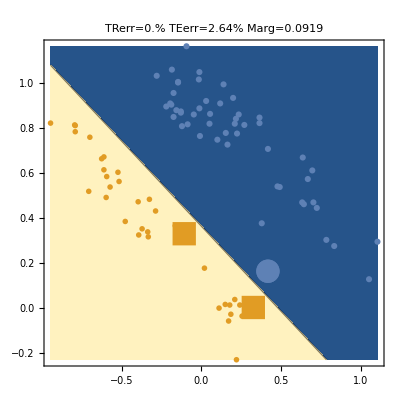

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
runSVMExperiment[fTr,yTr,fTe,yTe,trainHardMarginSVM,linearKernel]
```

As it can be seen, the decision surface, the margin and the training and testing error rates are exactly the same as the ones of the max-margin classifier introduced in the previous Section. However, the dual formulation used by SVMs allows to highlight the different role played by different training points: only the closest to the classification hyperplane become Support Vectors.

#### Soft-margin SVM

A soft-margin Support Vector Machine can be obtained by constructing the dual problem of the objective function in eq. (DisplayFormulaNumbered). In order to do this we first have to write down its generalized Lagrangian

L(w,b,ξ,α,r)=1/2(‖w‖)^2 +C ∑_(i=1)^n ξ_i+ ∑_(i=1)^n α_i(1-ξ_i-y_i(w·x_i+b))-∑_(i=1)^n r_i ξ_i.

We can then apply again Theorem 3 to obtain the KKT optimality conditions:

(∂L(w,b,ξ,α,r))/(∂w)=0
(∂L(w,b,ξ,α,r))/(∂b)=0
(∂L(w,b,ξ,α))/(∂ξ)=0
α_i(1-ξ_i-y_i(w·x_i+b))=0,       i=1,…,n
r_i ξ_i=0,                                               i=1,…,n
r_i≥0,                                                    i=1,…,n
α_i≥0,                                                    i=1,…,n

where the first three conditions expand to

w=∑_(i=1)^n α_i y_i x_i,
∑_(i=1)^n α_i y_i=0,
C-α_i=r_i,

and we note also that C-α_i=r_i, together with r_i≥0 and α_i≥0 gives us 0≤α_i≤C.
We can thus plug eq. (DisplayFormulaNumbered) into eq. (DisplayFormulaNumbered), to obtain

L(α)=1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j+C∑_(i=1)^n ξ_i+∑_(i=1)^n α_i-∑_(i=1)^n α_i ξ_i-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j -b(∑_(i=1)^n α_i y_i)_0-C∑_(i=1)^n ξ_i+∑_(i=1)^n α_i ξ_i
=∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j(x_i·x_j)
= ∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j H_(i,j),

where H_(i,j)=y_i y_j(x_i·x_j). As before, both w and b have disappeared from the Lagrangian, but once we have solved for α, we can compute w using eq. (DisplayFormulaNumbered), while b can again be obtained by enforcing the KKT complementarity condition α_i(1-ξ_i-y_i(w·x_i+b))=0.  Indeed if we expand this multiplication and left and right multiply by r_i we obtain:

α_i r_i-α_i(r_i ξ_i)_0-α_i r_i y_i(w·x_i+b)=0
α_i(1-y_i(w·x_i+b))=0,

which has the same solution: b=-(α̃ ᵀHα)/(1ᵀα) as before.
The Lagrangian dual program for the soft-margin SVM is thus given by

max_{α} 1ᵀα-1/2 αᵀHα
s.t. 0≤α≤C
	αᵀy=0

with b=-(α̃ ᵀHα)/(1ᵀα).
This dual optimization problem is identical to the one for hard-margin SVM, the only difference being the additional upper-bound constraint on α. As we can see, reducing the value of C has the effect of maxing-out the α_i, reducing the influence of the outliers (i.e. samples that due to noise lie in unexpected areas of the input space). Note also that with the choice C=∞ we would obtain the same results as for the hard-margin SVM.

Another important observation is that the primal KKT condition α_i(1-ξ_i-y_i(w·x_i+b))=0, implies that the only non-zero α_i can only be those for which y_i(w·x_i+b)+ξ_i=1, while the points with y_i(w·x_i+b)+ξ_i>1 will have α_i=0.
When C is decreased from ∞ (as in the case of hard-margin SVM) to some other finite value, the minimization of the ξ_i becomes relatively unimportant compared to the minimization of the squared norm of w, resulting in many samples being forced to have a large ξ_i. This means that by lowering the value of C, more and more samples will satisfy y_i(w·x_i+b)+ξ_i=1 (a reduction of the norm of w forces the optimization algorithm to compensate for the reduction of the functional margin, with an increase of ξ_i). In other words, lowering the value of C will result in an increased number of Support Vectors.

Using w=∑_(i=1)^n α_i y_i x_i, the minimal geometric margin can be computed as

g_S(f_(w,b))=1/(‖w‖)min_((x_i,y_i)∈S) y_i(w·x_i+b)
=(∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j)^(-1/2)min_((x_i,y_i)∈S) y_i(∑_(j=1)^n α_j y_j x_i·x_j+b).

#### Implementation in Mathematica

We hereby give a code snap implementing this algorithm, using the Mathematica QP solver where, as before, KTr is expected to be the matrix of inner products Ktr_(i,j)=x_i·x_j computed using the training samples

```mathematica
train1NormSoftMarginSVM[KTr_,yTr_,regC_]:=Module[
{nTr,d,H,f,a,alpha,b,nrm,margin,sol,obj,constraints},
{nTr,d}=Dimensions[KTr];
f=Table[1,{i,nTr}];
alpha=Table[Subscript[a, i],{i,nTr}];
H=yTr.Transpose[yTr] KTr;
constraints=First[alpha.yTr]==0 && (#>=0&/@(And@@alpha)) && 
(#<=regC&/@(And@@alpha));
obj=1/2 alpha.H.alpha - f.alpha;
sol=FindMinimum[{obj,constraints},alpha, Compiled->True, 
AccuracyGoal->1, PrecisionGoal->1, MaxIterations->100, 
Method -> "QuadraticProgramming", Gradient:> H.a - f];
alpha=(alpha/.sol[[2]]);
alpha[[Flatten@Position[#<10^(-8)&/@alpha,True]]]=0;
b=-1/Total[alpha] (alpha yTr[[All,1]]).H.alpha;
nrm=(2(sol[[1]]+Total[alpha]))^(1/2);
alpha=alpha yTr[[All,1]];
margin=(Min[(yTr(KTr.alpha+b))])/nrm;
{{alpha,b},margin}
];
```

An example of usage is also provided where, as before, the Support Vectors are marked with thiker markers (squares and circles), whille linearKernel is the function used to compute the inner products between the samples.

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train1NormSoftMarginSVM[#1,#2,10^c]&,linearKernel],{c,0,5,0.2}]
```

As we can see, the behavoir of the algorithm is pretty much the same as the soft-margin classifier introduced in the previous section. Moreover, according to what have seen before, as we reduce the regularization parameter C, the number of Support Vectors increases.

#### 2-Norm Soft-margin SVM

Another formulation for the Soft-margin SVM can be obtained considering the following modification of eq. (DisplayFormulaNumbered) in Section Section

min_(w,b,ξ) 1/2 w·w +C/2 ∑_(i=1)^n ξ_i^2
s.t. 1-ξ_i-y_i(w·x_i+b)≤0,   ∀(x_(i,)y_i)∈S,

where, for simplicity we have divided the objective function by two, and squared the slack variables, thus removing the necessity for the positivity constraints on the ξ_i. Due to the squaring of the slack variables, this is called the 2-Norm SVM. 
The generalized Lagrangian of this optimization problem is given by

L(w,b,ξ,α)=1/2(‖w‖)^2 +C/2 (‖ξ‖)^2+ ∑_(i=1)^n α_i(1-ξ_i-y_i(w·x_i+b))

and the KKT optimality conditions are given by

(∂L(w,b,ξ,α))/(∂w)=0
(∂L(w,b,ξ,α))/(∂b)=0
(∂L(w,b,ξ,α))/(∂ξ)=0
α_i(1-ξ_i-y_i(w·x_i+b))=0          i=1,…,n
α_i≥0,                                                    i=1,…,n

where the first three conditions expand to

w=∑_(i=1)^n α_i y_i x_i
∑_(i=1)^n α_i y_i=0
ξ=α/C

As before, since the optimization problem is convex and the constraints are affine functions, the KKT optimality conditions are also sufficient.
The Lagrangian dual problem is obtained by substituting the values of w and ξ back into L

L=1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j+1/(2C)∑_(i=1)^n ∑_(j=1)^n α_i α_j δ_(i,j)+∑_(i=1)^n α_i-1/C∑_(i=1)^n ∑_(j=1)^n α_i α_j δ_(i,j) -∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j -b(∑_(i=1)^n α_i y_i)_0
=∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j(x_i·x_j+1/C δ_(i,j))
= ∑_(i=1)^n α_i-1/2∑_(i=1)^n ∑_(j=1)^n α_i α_j H_(i,j),

where H_(i,j)=y_i y_j(x_i·x_j+1/C δ_(i,j)). As before, both w and b have disappeared from the Lagrangian, but w^* can then be obtained using eq. (DisplayFormulaNumbered),  while b can again be obtained by enforcing the KKT complementarity condition α_i(1-ξ_i-y_i(w·x_i+b))=0.  Indeed, we note that by substituting ξ_i with 1/c α_i, left and right multiplying the constraints α_i(1-ξ_i-y_i(w·x_i+b))=0 by y_i and summing over all i, we can enforce the constraint by commputing

∑_(i=1)^n α_i(y_i-1/c α_i y_i-∑_(j=1)^n α_j y_j x_j·x_i-b)=0
b∑_(i=1)^n α_i=(∑_(i=1)^n α_i y_i)_0-∑_(j=1)^n ∑_(i=1)^n α_i α_j y_i(1/c δ_(i,j))-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_j x_j·x_i
b=1/(∑_(i=1)^n α_i)(-∑_(i=1)^n ∑_(j=1)^n α_i α_j y_j(x_j·x_i+1/c δ_(i,j))) = 
=1/(1ᵀα)(-∑_(i=1)^n ∑_(j=1)^n α_i y_i α_j H_(i,j))=-(α̃ ᵀHα)/(1ᵀα),

where (α̃)_i=α_i y_i.
The Lagrangian dual problem can thus be defined as

max_{α} 1ᵀα-1/2 αᵀHα
s.t. α≥0
	αᵀy=0

with b=-(α̃ ᵀHα)/(1ᵀα). This optimization problem is once again very similar to the one for hard-margin SVM, the only difference being in the matrix H_(i,j)=y_i y_j(x_i·x_j+1/C δ_(i,j)), which is in this case augmented with an identity matrix multiplied by 1/C.  This has the effect of adding  1/C to the eigenvalues of the matrix, rendering the problem better conditioned. Note that, similarly to the 1-norm soft margin SVM, setting C→∞ would produce the same results as the hard margin SVM.

As stated before the minimal geometric margin g_S(f_(w,b)) of the soft-margin classifiers cannot be computed simply as 1/(‖w‖), since there is no guarantee anymore that y_i(w·x_i+b)≥ 1. Nonetheless, as before, for all the points for which y_i(w·x_i+b)<1 we will have y_i(w·x_i+b)=1-ξ_i, while for the others we will have ξ_i=0. Moreover, for the 2-norm soft margin SVM, by construction we have ξ_i=α_i/C and ∑_(i=1)^n α_i y_i=0, so that the minimal geometric margin can be computed exactly using g_S(f_(w,b))=1/(‖w‖)(1-(max_i α_i)/C), where

‖w‖=(∑_(i=1)^n ∑_(j=1)^n α_i α_j y_i y_j x_i·x_j)^(1/2)=(∑_(i=1)^n α_i y_i∑_(j=1)^n α_j y_j x_i·x_j)^(1/2)
=(∑_(i=1)^n α_i(1-ξ_i-y_i b))^(1/2)=(∑_(i=1)^n α_i-1/c∑_(i=1)^n α_i^2)^(1/2),

where again we have used the fact that for all the support vectors, α_i≠0→ξ_i≠0→y_i(w·x_i+b)=1-ξ_i.

#### Implementation in Mathematica

Since the only difference w.r.t. the hard margin is in the addition of the diagonal component to the H data matrix, we can reuse the code for the hard-margin SVM, with very little modifications, as shown by the following code snippet.

```mathematica
train2NormSoftMarginSVM[KTr_,yTr_,regC_]:=Module[{model,nrm,margin,nTr},
{nTr,nTr}=Dimensions[KTr];
{model,margin}=trainHardMarginSVM[KTr + 1/regC IdentityMatrix[nTr],yTr];
nrm=(margin^(-2) - 1/regC Norm[model[[1]]]^2)^(1/2);
margin = (1-Max[yTr model[[1]]]/regC)/nrm;
{model,margin}
];
```

As usual, we report here an example of usage of the considered classifier.

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train2NormSoftMarginSVM[#1,#2,10^c]&,linearKernel],{c,0,5,0.5}]
```

## Section. Kernel Support Vector Machines

### Kernel Methods

Linear-threshold algorithms, like max-margin classifiers and the SVM algorithms introduced in the previous section can only learn linear separation functions. However it is often the case that data is not separable by a simple linear hyperplane. In such cases, a separating hyperplane could still be found by non-linearly pre-mapping the original vectors x_i ∈ X into a new space φ(x_i ) ∈ F called the Feature Space, where the samples become linearly separable. A linear classifier can subsequently be trained in this space.

-Graphics-

Kernel methods allow to perform the mapping to an high-dimensional space, without  explicitly defining F and without explictly performing the mapping. 
In the remaining of this section, we will introduce the fundamental results from the Reproducing Kernel Hilbert Space theory, as presented also in [1].

#### Kernel function.

A function k(·, ·) that for all x, z ∈ X satisfies

k(x, z) = φ(x)· φ(z),

where φ is a mapping from X to an Hilbert space F and φ : x → φ(x) ∈ F is called kernel function. If X is an Hilbert space (e.g. an Euclidean space), the simplest example of kernel function is the one obtained considering the identity mapping φ(x) = x, in which case k(x, z) = x·z. 
A kernel function is thus a function that can be decomposed into a feature map φ to an Hilbert space F , applied to both arguments and followed by the evaluation of the inner product in F.

Advantages: if the kernel function is properly chosen, instances x_i can be implicitly mapped into a feature space of high (even infinite) dimensionality where they are possibly linearly separable (or better separable), without having to explicitly perform the expensive inner product evaluation in the expanded feature space.

#### Finitely positive semi-definite function.

Let X be a metric space, we say that a function: k :X ×X →ℝ is finitely positive semi-definite if it is a symmetric function and for all finite sets {x_1,x_2,…,x_n} ⊂ X , of size n, the n × n matrix K whose (i, j) entry is k(x_i, x_j) is positive semi-definite, formally

∀X, ∀ v ∈X⊂ℝ^n
vᵀKv ≥ 0.

The above mentioned matrix K is called Gramian matrix of k at x.

We can now state without proving the main result of the Reproducing Kernel Hilbert Space theory: the characterization Theorem of kernel functions.

#### Characterization of kernels.

A function k :X ×X →ℝ is a kernel function k(x, z) = φ(x)·φ(z) if and only if it satisfies the finitely positive semi-definite property.

#### Constructing kernels.

Let k_1 and k_2 be kernels over X ×X, X⊂ ℝ^n, a∈ℝ^+, f(·) a real function on X, ϕ:X→ℝ^m, with k_3 a kernel over ℝ^m×ℝ^m and B a symmetric positive semi-definite n×n matrix. The following functions are kernels:

k(x,z)=k_1(x,z)+k_2(x,z),
k(x,z)=ak_1(x,z),
k(x,z)=k_1(x,z)k_2(x,z),
k(x,z)=f(x)f(z),
k(x,z)=k_3(ϕ(x),ϕ(z)),
k(x,z)=xᵀBz.

Using these rules, it is possible to prove that the following functions are kernels [1]:

k(x,z)=p(k_1(x,z)),
k(x,z)=exp(k_1(x,z)),
k(x,z)=exp(-1/σ^2(‖x-z‖)^2),

where p is a polynomial with positive coefficient, σ∈ℝ^+ and the last kernel is called the Gaussian kernel.

#### Implementation in Mathematica

A snippet of code exploiting matrix computations to efficiently compute the Gaussian kernel (without any loop on the samples) is provided below

```mathematica
computeGaussianKernel[fTr_,fTe_,sigmaSQ_]:=Module[{D,K},
D=computeDist[fTr,fTe];
K=Exp[-1/(2 sigmaSQ) D]
];

computeDist[fTr_,fTe_]:=Module[{d,nTr,nTe,NTr,NTe,P,D},
{nTr,d}=Dimensions[fTr];
{nTe,d}=Dimensions[fTe];
P=fTr.Transpose[fTe];
NTr=Transpose[Table[Norm/@fTr, {i,nTe}]];
NTe=Table[Norm/@fTe, {i,nTr}];
D=NTr+NTe-2P
];
```

### Kernelized Support Vector Machines

“Kernel Trick”. Given an algorithm formulated in such a way that it depends on instances only through their inner product, it is possible to construct an alternative optimization problems by replacing the inner products with a kernel function.  The algorithm is thus said to be kernelizable.

As it can be seen from equations (DisplayFormulaNumbered,DisplayFormulaNumbered,DisplayFormulaNumbered), the SVM training procedures depends on data only via the inner products of the training instances, as encoded in the matrix H. We can thus substitute the inner products x_i·x_j in the matrix H, with evaluations of a kernel function k(x_i,x_j). The same argument can be repeated when computing b, while during prediction we have:

f_(w,b)(x_i)=w·x +b=∑_(j=1)^n α_j y_j x_j·x_i=∑_(j=1)^n α_j y_j k(x_j,x_i)+b,

The SVM algorithm is thus kernelizable.

#### Implementation in Mathematica

Following are two examples of using a Gaussian kernel with a 1-norm soft-margin SVM and σ either manually set

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train1NormSoftMarginSVM[#1,#2,10^c]&,gaussianKernel[10^s]],{c,0,6,0.5},{s,3,-1,-0.5}]
```

or automatically estimated from the distance matrix

```mathematica
createData[]
```

-Graphics-

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train1NormSoftMarginSVM[#1,#2,10^c]&,gaussianKernel[fTr]],{c,0,5,0.5}]
```

Note that the only difference w.r.t. 1-norm SVM implementation presented in the previous Section is that the linearKernel used to compute the inner products between the samples has been replaced with a gaussianKernel.
Examples with the 2-norm soft margin SVM and the hard-margin SVM can also be similarly obtained, without any modification to the training algorithm

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train2NormSoftMarginSVM[#1,#2,10^c]&,gaussianKernel[fTr]],{c,0,5,0.5}]
```

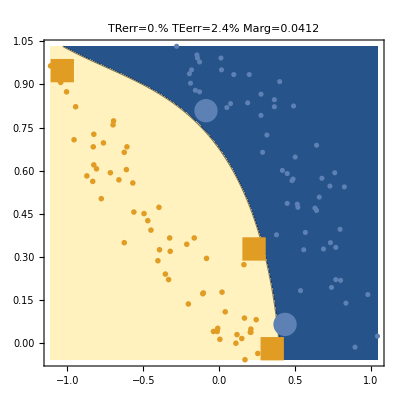

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
runSVMExperiment[fTr,yTr,fTe,yTe,trainHardMarginSVM,gaussianKernel[fTr]]
```

## Section. Conclusion

In this notebook we presented several max-margin and SVM classifiers, both in the linear and non-linear setting, partially following the exposition in [1]. We have exploited the Quadratic Programming functionality of Mathematica to solve most of the optimization problems presented. With the help of dynamic interactions, as dataset drawing and direct manipulation of the algorithm parameters, this Notebook can help understanding the algorithms and the role of their parameters.
The implementations provided here could virtually be used to address any binary classification problem. It is to note however, that in order to extend the applicability of the methods to larger problems (with more than a few hundreds of examples), it would be necessary to abandon the Mathematica QP solver and implement a Mathematica interface to existing and efficient C++ SVM implementations.

## References

1.	Nello Cristianini and John Shawe-Taylor. An introduction to Support Vector Machines and other kernel-based learning methods. Cambridge university press, 2000